```mathematica
data=Import["/Users/daniel/Documents/Columbia/Research/Kipping/papers/koi3678_paper/lombscargle/times_input.txt","Table"];
```

```mathematica
lin=LinearModelFit[data[[2;;All,{1,2}]],{t},t];
P0=lin["ParameterTableEntries"][[All,1]][[2]];
τ0=lin["ParameterTableEntries"][[All,1]][[1]];
```

```mathematica
fn[τ_,P_,α_,β_,Pttv_,t_]:=τ+P t+α Sin[(2π t)/Pttv]+β Cos[(2π t)/Pttv]
χ2[τ_,P_,α_,β_,Pttv_,datain_]:=Sum[((fn[τ,P,α,β,Pttv,datain[[i,1]]]-datain[[i,2]])/datain[[i,3]])^2,{i,1,Length[datain]}];
```

### Without last point, standard LS

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

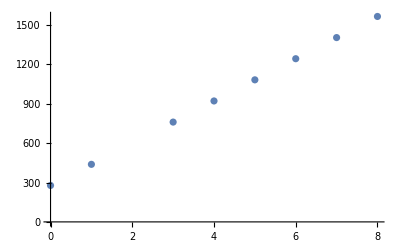

```mathematica
input=data[[2;;Length[data]-1]];
<<ErrorBarPlots`
ErrorListPlot[input,PlotRange->All]
```

```mathematica
Pmax=2(Max[input[[All,1]]]-Min[input[[All,1]]]);
Pmin=2;
fmax=1/Pmin;fmin=1/Pmax;
fgrid=Table[f,{f,fmin,fmax,0.1fmin}];
Pgrid=N[Sort[Table[1/fgrid[[i]],{i,1,Length[fgrid]}]][[2;;All]]];
```

469.005

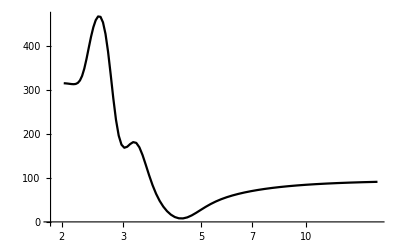

```mathematica
nullfit=LinearModelFit[input[[All,{1,2}]],{t},t,IncludeConstantBasis->True,Weights->input[[All,3]]^-2];
nullparams=nullfit["ParameterTableEntries"][[All,1]];
nullχ2trunc=χ2[nullparams[[1]],nullparams[[2]],0,0,2,input]
j=0;Label[jloop];j=j+1;lm=LinearModelFit[input[[All,{1,2}]],{t,Sin[(2π t)/Pgrid[[j]]],Cos[(2π t)/Pgrid[[j]]]},t,IncludeConstantBasis->True,Weights->input[[All,3]]^-2];params=lm["ParameterTableEntries"][[All,1]];Subscript[Δχ2, j]=nullχ2trunc-χ2[params[[1]],params[[2]],params[[3]],params[[4]],Pgrid[[j]],input];If[j<Length[Pgrid],Goto[jloop]];
LSperiodogramtrunc=Table[{Pgrid[[j]],Subscript[Δχ2, j]},{j,1,Length[Pgrid]}];
Pbesttrunc=Sort[LSperiodogramtrunc,#1[[2]]>#2[[2]]&][[1]][[1]];
ListLogLinearPlot[LSperiodogramtrunc,Joined->True,PlotStyle->Black]
```

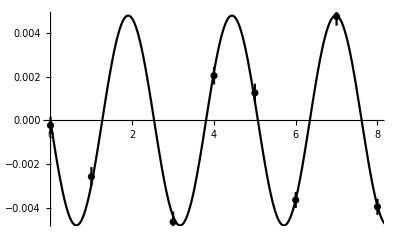

```mathematica
lmbesttrunc=LinearModelFit[input[[All,{1,2}]],{t,Sin[(2π t)/Pbesttrunc],Cos[(2π t)/Pbesttrunc]},t,IncludeConstantBasis->True,Weights->input[[All,3]]^-2];
times=Table[{input[[i,1]],input[[i,2]]-(lmbesttrunc["ParameterTableEntries"][[All,1]][[1]]+lmbesttrunc["ParameterTableEntries"][[All,1]][[2]]*input[[i,1]]),input[[i,3]]},{i,1,Length[input]}];
Show[ErrorListPlot[times,PlotRange->All,PlotStyle->Black],Plot[lmbesttrunc["ParameterTableEntries"][[All,1]][[3]] Sin[(2π t)/Pbesttrunc]+lmbesttrunc["ParameterTableEntries"][[All,1]][[4]] Cos[(2π t)/Pbesttrunc],{t,0,30},PlotStyle->Black]]
```

### With all data

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

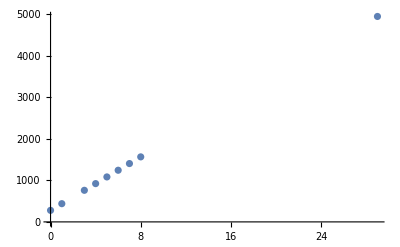

```mathematica
input=data[[2;;All]];
<<ErrorBarPlots`
ErrorListPlot[input,PlotRange->All]
```

```mathematica
Pmax=2(Max[input[[All,1]]]-Min[input[[All,1]]]);
Pmin=2;
fmax=1/Pmin;fmin=1/Pmax;
fgrid=Table[f,{f,fmin,fmax,0.1fmin}];
Pgrid=N[Sort[Table[1/fgrid[[i]],{i,1,Length[fgrid]}]][[2;;All]]];
```

534.345

53.6091

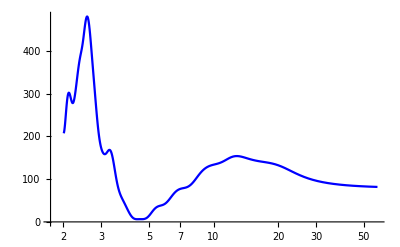

```mathematica
nullfit=LinearModelFit[input[[All,{1,2}]],{t},t,IncludeConstantBasis->True,Weights->input[[All,3]]^-2];
nullparams=nullfit["ParameterTableEntries"][[All,1]];
nullχ2=χ2[nullparams[[1]],nullparams[[2]],0,0,2,input]
j=0;Label[jloop];j=j+1;lm=LinearModelFit[input[[All,{1,2}]],{t,Sin[(2π t)/Pgrid[[j]]],Cos[(2π t)/Pgrid[[j]]]},t,IncludeConstantBasis->True,Weights->input[[All,3]]^-2];params=lm["ParameterTableEntries"][[All,1]];Subscript[Δχ2, j]=nullχ2-χ2[params[[1]],params[[2]],params[[3]],params[[4]],Pgrid[[j]],input];If[j<Length[Pgrid],Goto[jloop]];
LSperiodogram=Table[{Pgrid[[j]],Subscript[Δχ2, j]},{j,1,Length[Pgrid]}];
Pbest=Sort[LSperiodogram,#1[[2]]>#2[[2]]&][[1]][[1]];
lowestχ2=nullχ2-Sort[LSperiodogram,#1[[2]]>#2[[2]]&][[1]][[2]]
ListLogLinearPlot[LSperiodogram,Joined->True,PlotStyle->Blue]
```

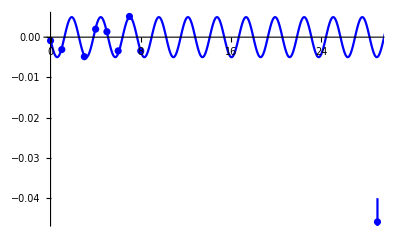

```mathematica
lmbest=LinearModelFit[input[[All,{1,2}]],{t,Sin[(2π t)/Pbest],Cos[(2π t)/Pbest]},t,IncludeConstantBasis->True,Weights->input[[All,3]]^-2];
times=Table[{input[[i,1]],input[[i,2]]-(lmbest["ParameterTableEntries"][[All,1]][[1]]+lmbest["ParameterTableEntries"][[All,1]][[2]]*input[[i,1]]),input[[i,3]]},{i,1,Length[input]}];
Show[ErrorListPlot[times,PlotRange->All,PlotStyle->Blue],Plot[lmbest["ParameterTableEntries"][[All,1]][[3]] Sin[(2π t)/Pbest]+lmbest["ParameterTableEntries"][[All,1]][[4]] Cos[(2π t)/Pbest],{t,0,30},PlotStyle->Blue]]
```

### With all data + sine wave

```mathematica
fnfast[τ_,P_,α_,β_,αf_,βf_,Pttv_,Pttvfast_,t_]:=τ+P t+α Sin[(2π t)/Pttv]+β Cos[(2π t)/Pttv]+αf Sin[(2π t)/Pttvfast]+βf Cos[(2π t)/Pttvfast]
χ2fast[τ_,P_,α_,β_,αf_,βf_,Pttv_,Pttvfast_,datain_]:=Sum[((fnfast[τ,P,α,β,αf,βf,Pttv,Pttvfast,datain[[i,1]]]-datain[[i,2]])^2/(datain[[i,3]])^2),{i,1,Length[datain]}];
```

```mathematica
input=data[[2;;All]];
<<ErrorBarPlots`
ErrorListPlot[input,PlotRange->All]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

-Graphics-

```mathematica
Pmax=2(Max[input[[All,1]]]-Min[input[[All,1]]]);
Pmin=2;
fmax=1/Pmin;fmin=1/Pmax;
fgrid=Table[f,{f,fmin,fmax,0.1fmin}];
Pgrid=N[Sort[Table[1/fgrid[[i]],{i,1,Length[fgrid]}]][[2;;All]]];
```

24.1667

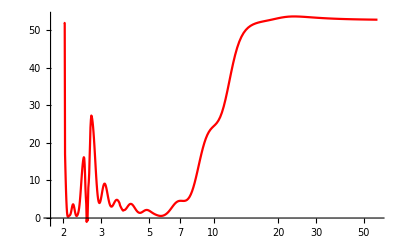

```mathematica
initial={lmbest["ParameterTableEntries"][[All,1]][[1]],lmbest["ParameterTableEntries"][[All,1]][[2]],lmbest["ParameterTableEntries"][[All,1]][[3]],lmbest["ParameterTableEntries"][[All,1]][[4]],0,0,Pbest};
j=0;Label[jloop];j=j+1;sol=NMinimize[χ2fast[τ,P,α,β,αf,βf,Pgrid[[j]],Pttvfast,input],{τ,P,α,β,αf,βf,Pttvfast},Method->{"NelderMead","InitialPoints"->{initial}}];Subscript[Δχ2, j]=lowestχ2-sol[[1]];If[j<Length[Pgrid],Goto[jloop]];
LSslowperiodogram=Table[{Pgrid[[j]],Subscript[Δχ2, j]},{j,1,Length[Pgrid]}];
Pslowbest=Sort[LSslowperiodogram,#1[[2]]>#2[[2]]&][[1]][[1]]
ListLogLinearPlot[LSslowperiodogram,Joined->True,PlotStyle->Red]
```

```mathematica
initial={lmbest["ParameterTableEntries"][[All,1]][[1]],lmbest["ParameterTableEntries"][[All,1]][[2]],lmbest["ParameterTableEntries"][[All,1]][[3]],lmbest["ParameterTableEntries"][[All,1]][[4]],0,0,Pbest};
solbest=NMinimize[χ2fast[τ,P,α,β,αf,βf,Pslowbest,Pttvfast,input],{τ,P,α,β,αf,βf,Pttvfast},Method->{"NelderMead","InitialPoints"->{initial}}]
```

{0.0163927,{τ→277.513,P→160.883,α→0.00400571,β→-0.00693635,αf→-0.004698,βf→-0.000725353,Pttvfast→2.5802}}

```mathematica
solbest[[2]][[All,2]][[1]]
```

277.513

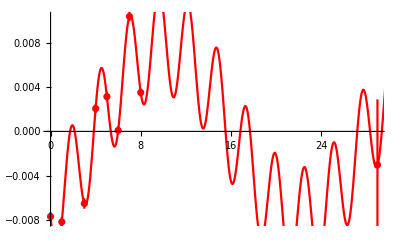

```mathematica
"Looks a bit funky because of the new linear ephemeris picked";
times=Table[{input[[i,1]],input[[i,2]]-(solbest[[2]][[All,2]][[1]]+solbest[[2]][[All,2]][[2]]*input[[i,1]]),input[[i,3]]},{i,1,Length[input]}];
Show[ErrorListPlot[times,PlotRange->All,PlotStyle->Red],Plot[fnfast[0,0,solbest[[2]][[All,2]][[3]],solbest[[2]][[All,2]][[4]],solbest[[2]][[All,2]][[5]],solbest[[2]][[All,2]][[6]],Pslowbest,solbest[[2]][[All,2]][[7]],t],{t,0,30},PlotStyle->Red]]
```

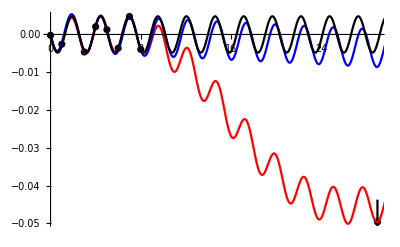

```mathematica
"Same plot but now forcing it onto the original Kepler truncated lin ephemeris";
times=Table[{input[[i,1]],input[[i,2]]-(lmbesttrunc["ParameterTableEntries"][[All,1]][[1]]+lmbesttrunc["ParameterTableEntries"][[All,1]][[2]]*input[[i,1]]),input[[i,3]]},{i,1,Length[input]}];
Show[ErrorListPlot[times,PlotRange->All,PlotStyle->Black],Plot[fnfast[solbest[[2]][[All,2]][[1]]-lmbesttrunc["ParameterTableEntries"][[All,1]][[1]],solbest[[2]][[All,2]][[2]]-lmbesttrunc["ParameterTableEntries"][[All,1]][[2]],solbest[[2]][[All,2]][[3]],solbest[[2]][[All,2]][[4]],solbest[[2]][[All,2]][[5]],solbest[[2]][[All,2]][[6]],Pslowbest,solbest[[2]][[All,2]][[7]],t],{t,0,30},PlotStyle->Red],Plot[(lmbest["ParameterTableEntries"][[All,1]][[1]]-lmbesttrunc["ParameterTableEntries"][[All,1]][[1]])+(lmbest["ParameterTableEntries"][[All,1]][[2]]-lmbesttrunc["ParameterTableEntries"][[All,1]][[2]]) t+lmbest["ParameterTableEntries"][[All,1]][[3]] Sin[(2π t)/Pbest]+lmbest["ParameterTableEntries"][[All,1]][[4]] Cos[(2π t)/Pbest],{t,0,30},PlotStyle->Blue],Plot[lmbesttrunc["ParameterTableEntries"][[All,1]][[3]] Sin[(2π t)/Pbesttrunc]+lmbesttrunc["ParameterTableEntries"][[All,1]][[4]] Cos[(2π t)/Pbesttrunc],{t,0,30},PlotStyle->Black]]
```

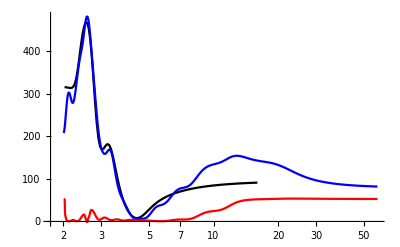

```mathematica
ListLogLinearPlot[{LSperiodogramtrunc,LSperiodogram,LSslowperiodogram},Joined->True,PlotStyle->{Black,Blue,Red}]
```